-Graphics-

# How to reshape data

## Clean, manipulate and reshape imported data in Wolfram Language

-Graphics-

## Built-in data structures

List

Association

## Association

Association is like a List, but you use keys to refer to values instead of numbers

```mathematica
{1, 2, 3}[[2]]
```

2

```mathematica
<|"a" -> 1, "b" ->2, "c" -> 3|>[["a"]]
```

1

Part extraction

```mathematica
data = {<|"a"-><|"a"->"a1"|>,"b"-><|"b"->"b1"|>|>, <|"a"-><|"a"->"a2"|>,"b"-><|"b"->"b2"|>|>};
data[[All, All, "a"]]
```

{<|a→a1,b→Missing[KeyAbsent,a]|>,<|a→a2,b→Missing[KeyAbsent,a]|>}

Functions specifics for Association

```mathematica
Keys[<|"a" -> 1|>]
```

```mathematica
Values[<|"a" -> 1|>]
```

```mathematica
Lookup[<|"a" -> 1|>, "a"]
```

```mathematica
KeyTake[<|a->1,b->2,c->3|>,{a,b}]
```

```mathematica
KeyDrop[<|a->1,b->2|>,a]
```

```mathematica
KeyValueMap[f,<|a->1,b->2,c->3|>]
```

```mathematica
MapIndexed[f,<|a->1,b->2,c->3|>]
```

```mathematica
Merge[{<|a->1,b->2|>,<|b->4,c->5|>},Identity]
```

```mathematica
Merge[{<|a->1,b->2|>,<|a->5,b->10|>},Total]
```

## Importing sample data

Create data on your machine.

```mathematica
folder = FileNameJoin[{NotebookDirectory[], "data"}];
CreateDirectory[folder];

data = ;

Export[
FileNameJoin[{folder, "persons.csv"}] ,
Join[{Keys@First@data}, Values @ data]
]

SeedRandom[1];

users = data[[All, "id"]];
probs = AssociationMap[RandomSample@Table[i^8, {i, Length[users]}]&,users];

transactions = Table[
Export[
FileNameJoin[{folder, "2016-10-" <> ToString[i]<>".csv"}],
Join[
{{"from", "to", "amount"}},
Table[
With[{u = RandomChoice[users]}, {u, RandomChoice[probs[u] -> Range[Length[users]]]}] ~ Join ~ {ToString @ AccountingForm[RandomReal[{1000, 4000}],NumberPoint->",", NumberSeparator -> ".", DigitBlock->3]},
{j, RandomInteger[{5, 15}]}
]
]
], 
{i, 30}
];
```

CreateDirectory::filex: /Users/rdv/Desktop/data already exists.

/Users/rdv/Desktop/data/persons.csv

Manually inspect data

```mathematica
SystemOpen[folder]
```

Import the data

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]]
```

## Possible representations

Lists of Lists

```mathematica
{
{1,"Deanna Gardner","F",30,57,167,"ECP-8254"},
{2,"Brian Rodriguez","M",42,71,174,"50BH7"}
}
```

Association of lists

```mathematica
<|
"full_name"->{"Rebecca Burke","Brian Taylor","Heather Watkins","Chris Villegas"},
"sex"->{"F","M","F","M"}
|>
```

List of associations

```mathematica
{
<|"sex"->"F","full_name"->"Deanna Gardner"|>,
<|"sex"->"M","full_name"->"Brian Rodriguez"|>,
<|"sex"->"F","full_name"->"Rebecca Burke"|>
}
```

## Lists of lists

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
data = Rest @ csv
```

```mathematica
data[[All, 2]]
```

```mathematica
Rule @@@ data[[All, {2, 4}]]
```

Advantages

very small size for large data

efficient structure

Disadvantages

your code is unreadable

## Association with lists

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
headers = First@csv;
data = Rest @ csv;
```

```mathematica
grouped = AssociationThread[headers -> Transpose[data]]
```

```mathematica
grouped[[{"id", "sex"}, 1]]
```

<|id→1,sex→F|>

```mathematica
grouped[[{"full_name", "sex"}, {3, 4, 5, 6}]]
```

Advantages

code is now readable, you can now refer to columns in the code

efficient structure

Disadvantages

working with list of arrays might be counter-intuitive

#### rollback to list of lists

```mathematica
Values @ grouped
```

## Lists of association

```mathematica
csv = Import[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
headers = First@csv;
data = Rest @ csv;
```

#### method 1

```mathematica
grouped = Map[AssociationThread[headers -> #] &, data];
```

#### method 2

```mathematica
grouped =Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads->All];
```

```mathematica
grouped[[All, "sex"]]
```

{F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M,F,M}

```mathematica
grouped[[All, {"sex", "fullname"}]]
```

Advantages

you can still think in terms of lists of lists

Disadvantages

can be memory inefficient for very large datasets

#### rollback to list of lists

```mathematica
Values @ grouped
```

## Merging multiple csv

```mathematica
SystemOpen[folder]
```

```mathematica
names = FileNames["2016-*.csv", folder];
```

```mathematica
Map[FileBaseName[#] &, names]
```

```mathematica
Interpreter["StructuredDate"][Map[FileBaseName, names]];
```

```mathematica
Map[StringSplit[FileBaseName@#, "-"] &, names]
```

```mathematica
dates = Map[DateObject[FromDigits /@ StringSplit[FileBaseName[#], "-"]] &, names]
```

```mathematica
reshape[csv_String] := reshape[Import[csv, "CSV"]]
reshape[csv_List] := With[
{headers = First[csv], data = Rest[csv]},
Transpose[AssociationThread[headers -> Transpose[data]], AllowedHeads->All]
]
```

```mathematica
transactions = Apply[
Function[
{date, csv},
reshape[csv]
],
Transpose[{dates, names}],
{1}
];
```

```mathematica
transactions = Flatten @ Apply[
Function[
{date, csv},
Map[Append[#, "date" -> date]&,reshape[csv]]
],
Transpose[{dates, names}],
{1}
];
```

```mathematica
fixAmount[s_String] := ToExpression@StringReplace[s,{ "." -> "",  "," -> "."}]
fixAmount[s_] := s
```

```mathematica
transactions = Flatten @ Apply[
Function[
{date, csv},
Map[Append[#, {"date" -> date, "amount" -> fixAmount[#amount]}]&,reshape[csv]]
],
Transpose[{dates, names}],
{1}
];
```

## Merging all data

```mathematica
transactions;
```

```mathematica
persons = reshape[FileNameJoin[{NotebookDirectory[], "data", "persons.csv"}]];
```

```mathematica
getTransactions[id_, key_:"from"] := 
Select[
transactions, 
Function[
{t},
id == t[key]
]
]
```

```mathematica
merged = Map[
Append[
#, {
"outgoing" -> getTransactions[#id, "from"],
"incoming" -> getTransactions[#id, "to"]
}
] &,
persons
];
```

## Querying the data

```mathematica
Dataset @ merged
```

```mathematica
merged[[1]]
```

```mathematica
merged[[1, "outgoing", All, "amount"]]
```

{142852,317039,313452,384.59,210846,206385,118236,335.76,284607,168534,222878,212134,244797,137689,213.31,335689,329873,264.82,344055,308475}

```mathematica
PieChart[
Map[
Total[#[["outgoing", All, "amount"]]]&,
merged
],
ChartLabels->merged[[All, "fullname"]]
]
```

-Graphics-

## Example graph

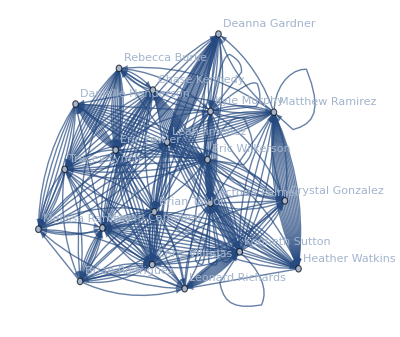

```mathematica
makeGraph[tr_] := Graph[
Map[
Labeled[#id, #["fullname"]] &,
persons
],
Map[
#from -> #to &,
tr
]
]
makeGraph[transactions]
```

```mathematica
Manipulate[
makeGraph[Select[transactions,#date === i &]],
{i, DeleteDuplicates[transactions[[All, "date"]]]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["date"]];
Manipulate[
makeGraph[regroup[i]],
{i, Keys[regroup]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["date"], makeGraph];
Manipulate[
regroup[i],
{i, Keys[regroup]},
ControlType->Slider
]
```

```mathematica
regroup = GroupBy[transactions, Key["from"], makeGraph];
Manipulate[
regroup[i],
{i, Keys[regroup]},
ControlType->Slider
]
```